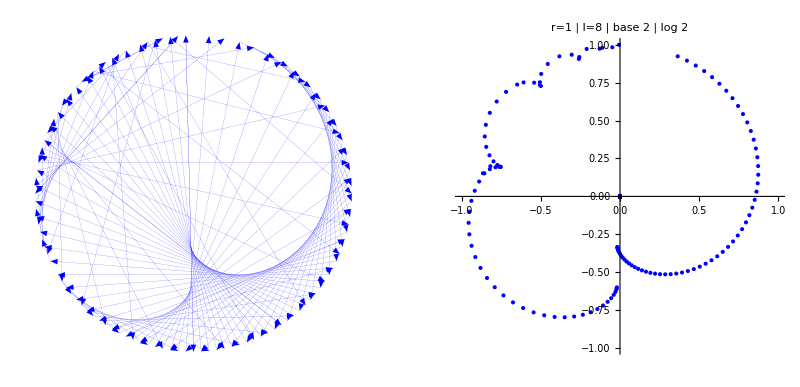

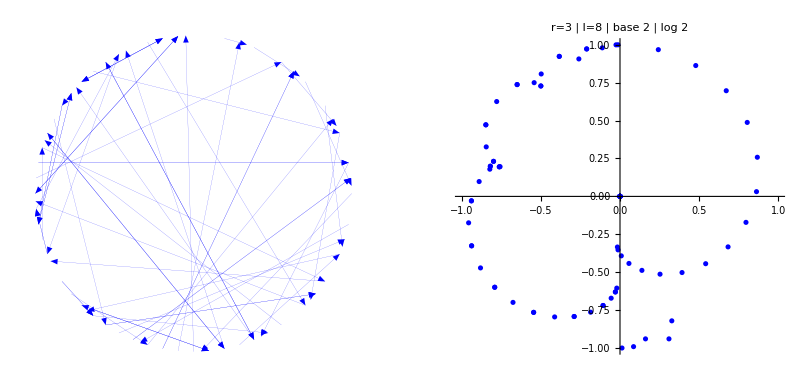

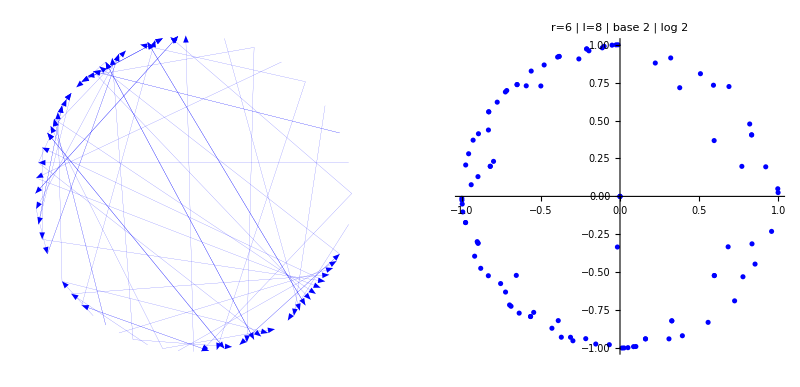

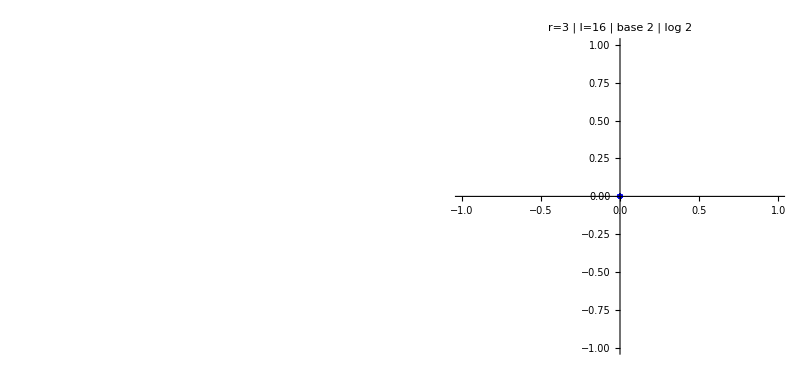

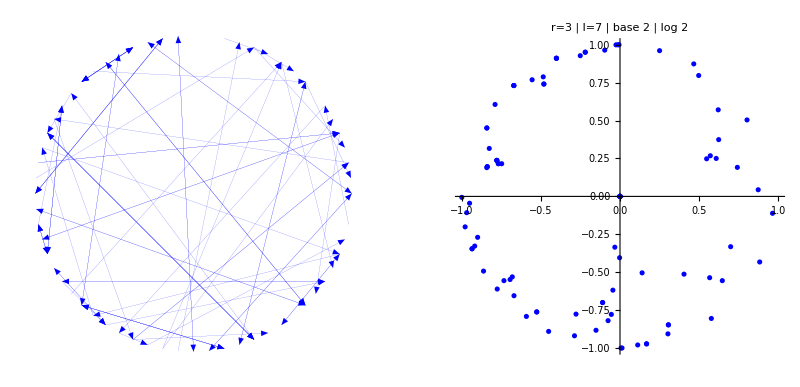

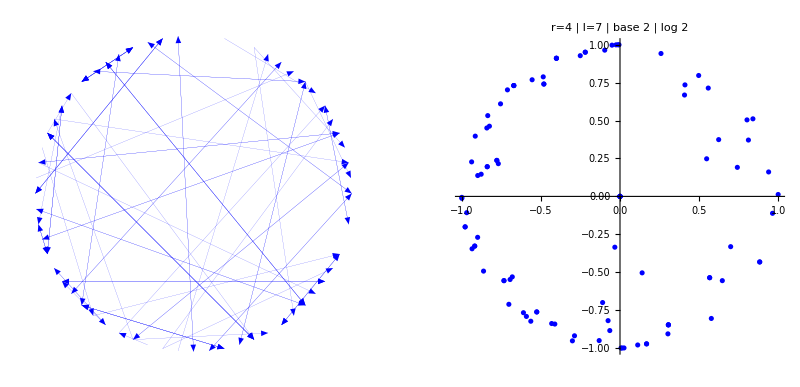

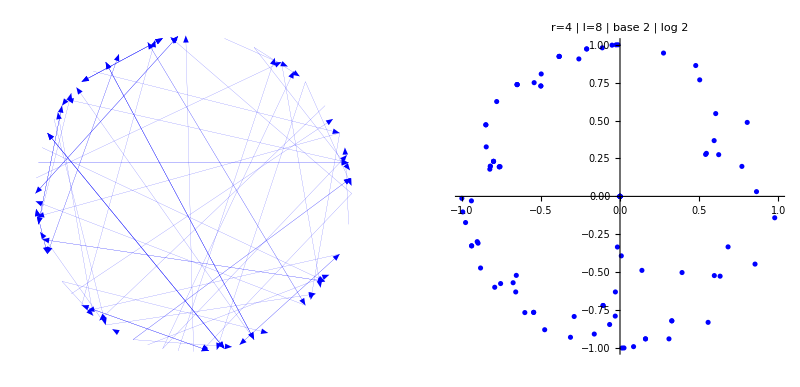

```mathematica
ClearAll["Global`*"];
r[t_]:=(x=-Sin[t];y=Cos[t];{x,y});

rotateLeft[n_,r_,l_]:=Mod[n*2^r,2^l-1];

intersectLines[line1_,line2_]:=(
a11=line1[[1,2]]-line1[[2,2]];a12=line1[[2,1]]-line1[[1,1]];det1=Det[line1];a21=line2[[1,2]]-line2[[2,2]];a22=line2[[2,1]]-line2[[1,1]];det2=Det[line2];
Quiet[Check[LinearSolve[{{a11,a12},{a21,a22}},{-det1,-det2}],{0,0}]]
);

generatePlot[f_,g_, start_,stop_,step_, label_]:= (
e=0.001;
lines1=Table[{r[2Pi*g[t]],r[2Pi*g[f[t]]]},{t,start,stop,step}];
lines2=Table[{r[2Pi*g[t+e]],r[2Pi*g[f[t+e]]]},{t,start,stop,step}];
plot1=Graphics[{Blue, Thickness[0.0001],Map[Arrow,lines1],PlotRange->{{-1,1},{-1,1}},AspectRatio->1, PlotLabel->label}];
plot2=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1, PlotLabel->label,PlotStyle->Blue];
GraphicsGrid[{{plot1,plot2}}]
);

f[x_]:=rotateLeft[x,1,8];
g[x_]:=x/2^Floor[Log[2,x]];
generatePlot[f, g,1,250,1, "r=1 | l=8 | base 2 | log 2"]

f[x_]:=rotateLeft[x,3,8];
g[x_]:=x/2^Floor[Log[2,x]];
generatePlot[f, g,1,100,1, "r=3 | l=8 | base 2 | log 2"]

f[x_]:=rotateLeft[x,6,8];
g[x_]:=x/2^Floor[Log[2,x]];
generatePlot[f, g,1,100,1, "r=6 | l=8 | base 2 | log 2"]

f[x_]:=rotateLeft[x,3,16];
g[x_]:=x/2^Floor[Log[2,x]];
generatePlot[f, g,1,100,1, "r=3 | l=16 | base 2 | log 2"]

f[x_]:=rotateLeft[x,3,7];
g[x_]:=x/2^Floor[Log[2,x]];
generatePlot[f, g,1,100,1, "r=3 | l=7 | base 2 | log 2"]

f[x_]:=rotateLeft[x,4,7];
g[x_]:=x/2^Floor[Log[2,x]];
generatePlot[f, g,1,100,1, "r=4 | l=7 | base 2 | log 2"]

f[x_]:=rotateLeft[x,4,8];
g[x_]:=x/2^Floor[Log[2,x]];
generatePlot[f, g,1,100,1, "r=4 | l=8 | base 2 | log 2"]

(*f[x_]:=rotateLeft[x,3,Floor[Log2[x]]+1];
g[x_]:=x/2^Floor[Log[2,x]];
generatePlot[f, g,50,100,1, "r=3 | l=8 | base 2 | log 2"]*)
```